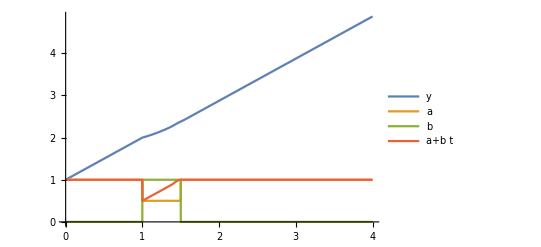

```mathematica
sol=NDSolve[{y'[t]==s[t],s[t]==a[t]+b[t]( t-1),WhenEvent[t==1,{a[t]->0.5,b[t]->1}],
WhenEvent[t==1.5,{a[t]->1,b[t]->0}],
y[0]==1,a[0]==1,b[0]==0},{y,a,b,s},{t,0,4},DiscreteVariables->{a,b}];
Plot[Evaluate[{y[t],a[t],b[t],s[t]}/.sol],{t,0,4},PlotLegends->LineLegend[{"y","a","b","a+b t"}]]
```

```mathematica
ClearAll["Global`*"]
SetOptions[Plot,ImageSize->350];

PLOTSTYLE:={
Directive[Magenta,AbsoluteThickness[2]],
Directive[Black,AbsoluteThickness[2]],
Directive[Magenta,AbsoluteThickness[1]],
Directive[Black,AbsoluteThickness[1]]}

Manipulate[Module[{sol = NDSolve[
{

(*Price shock as variable shock,
 Variable shock for p[t] at time tp, p[t] jumps to fpp x p[t] at time tp*)
WhenEvent[t==tp,{p[t]->fpp p[t]}],

(*Demand shock as variable shock,
 Variable shock for C[t] at time tnc, C[t] jumps to fnc x c[t] at time tnc*)
WhenEvent[t==tnc,{c[t]->fnc c[t]}],



(* Demand shock as model shock (shock of power of household),
Model shock for μHc[t] at time tn, decays over the time period of dn,
σnμHc[t] a sawtooth curve,
σnμHc[0]=1, jumps at time tn to fnμHc, goes back linearly to 1 in the time period of dn,
μHc[t]=μHc x σnμHc[t] a sawtooth curve,
μHc[0]=μHc, jumps at time tn to μHc x fnμHc, goes back linearly to μHc in the time period of dn *)

σnμHc[t]==σnμHc0[t]+σnμHc1[t] (t-tn),
σnμHc0[0]==1,σnμHc1[0]==0,
WhenEvent[t==tn,{σnμHc0[t]->fnμHc,σnμHc1[t]->(1-fnμHc)/dn}],
WhenEvent[t==tn+dn,{σnμHc0[t]->1,σnμHc1[t]->0}],

(* Supply shock as model shock (shock of power of firm),
Model shock for μFk[t] at time ta, decays over the time period of da,
σaμFk[t] a sawtooth curve,
σaμFk[0]=1, jumps at time tn to faμFk, goes back linearly to 1 in the time period of da,
μFk[t]=μFk x σaμFk[t] a sawtooth curve,
μFk[0]=μFk, jumps at time ta to μFk x faμFk, goes back linearly to μFk in the time period of da *)

σaμFk[t]==σaμFk0[t]+σaμFk1[t] (t-ta),
σaμFk0[0]==1,σaμFk1[0]==0,
WhenEvent[t==ta,{σaμFk0[t]->faμFk,σaμFk1[t]->(1-faμFk)/da}],
WhenEvent[t==ta+da,{σaμFk0[t]->1,σaμFk1[t]->0}],

(*Supply shock as model shock (technology shock),
Model shock for β[t] at time taβ, decays over the time period of daβ ,
σaβ[t] a sawtooth curve,
σaβ[0]=1, jumps at time taβ to faβ, goes back linearly to 1 in the time period of daβ,
β[t]=β x σaβ[t] a sawtooth curve,
β[0]=β, springt zum Zeitpunkt taβ auf β x faβ, goes back linearly to β in the time period of daβ *)

σaβ[t]==σaβ0[t]+σaβ1[t] (t-taβ),
σaβ0[0]==1,σaβ1[0]==0,
WhenEvent[t==taβ,{σaβ0[t]->faβ,σaβ1[t]->(1-faβ)/daβ,c[t]->faβ c[t],k'[t]->faβ k'[t]}],
WhenEvent[t==taβ+daβ,{σaβ0[t]->1,σaβ1[t]->0}],

(* GCD equationsystem adapted to shocks*)
y[t]==β σaβ[t] k[t]^(1-α) l[t]^α ,

c'[t]==γ μHc σnμHc[t] c[t]^(-1+γ)-p[t] Subscript[λ, 1][t]+p[t] Subscript[λ, 2][t]-Subscript[λ, 3][t],
k'[t]==(1-α) β σaβ[t]μFk σaμFk[t] k[t]^-α l[t]^α p[t]-Subscript[λ, 3][t],
l'[t]==2 μHl (ldach-l[t])+μFl (α β σaβ[t] k[t]^(1-α) l[t]^(-1+α) p[t]-w[t])+w[t] Subscript[λ, 1][t]-w[t] Subscript[λ, 2][t]+α β σaβ[t] k[t]^(1-α) l[t]^(-1+α) Subscript[λ, 3][t],
mh'[t]==2 μHmh (mhdach-mh[t])-Subscript[λ, 1][t],
p'[t]==β σaβ[t]μFp k[t]^(1-α) l[t]^α-c[t] Subscript[λ, 1][t]+c[t] Subscript[λ, 2][t],
s'[t]==2 μFs (sdach-s[t])-Subscript[λ, 3][t],
w'[t]==-μFw l[t]+l[t] Subscript[λ, 1][t]-l[t] Subscript[λ, 2][t],
mb'[t]==-Subscript[λ, 2][t],
0==-c[t] p[t]+l[t] w[t]-mh'[t],
0==c[t] p[t]-l[t] w[t]-mb'[t],
0==-c[t]+β σaβ[t] k[t]^(1-α) l[t]^α-k'[t]-s'[t],

c[0]==k0^(1-α) l0^α β ,k[0]==k0,l[0]==l0,mb[0]==mb0,mh[0]==mh0,p[0]==p0,s[0]==s0,w[0]==w0
},

{σnμHc,σnμHc0,σnμHc1,σaμFk,σaμFk0,σaμFk1,σaβ,σaβ0,σaβ1,c,k,l,mb,mh,p,s,w,y,Subscript[λ, 1],Subscript[λ, 2],Subscript[λ, 3]},{t,0,tmax},
MaxStepSize->0.01,
DiscreteVariables->{σnμHc0,σnμHc1,σaμFk0,σaμFk1,σaβ0,σaβ1}]},


{Plot[Evaluate[{c[t],k[t],l[t],mb[t],mh[t],p[t],s[t],w[t],y[t]}/.sol],
{t,0,tmax},
PlotRange->{-1,plotmax},
PlotLabels->{"c","k[t]","l[t]","mb[t]","mh[t]","p[t]","s[t]","w[t]","y[t]"},
PlotLegends->LineLegend[{"c","k[t]","l[t]","mb[t]","mh[t]","p[t]","s[t]","w[t]","y[t]"}]
],

Plot[Evaluate[{c[t],k'[t],s'[t],y[t],-c[t] p[t]+l[t] w[t]-mh'[t]+2,c[t] p[t]-l[t] w[t]-mb'[t]+2.2,y[t]-c[t]-k'[t]-s'[t]+2.4}/.sol],
{t,0,tmax},
PlotRange->{-1,plotmax},
PlotLabels->{"c","k'[t]","s'[t]","y[t]","ZB1+2","ZB2+2.2","ZB3+2.4"},
PlotLegends->LineLegend[{"c","k'[t]","s'[t]","y[t]","ZB1+2","ZB2+2.2","ZB3+2.4"}]
],

Plot[Evaluate[{σnμHc1[t],σnμHc0[t],σnμHc[t]+1,σaμFk1[t]+3,σaμFk0[t]+3,σaμFk[t]+4,σaβ1[t]+6,σaβ0[t]+6,σaβ[t]+7}/.sol],
{t,0,tmax},
PlotRange->{0,9},
PlotLabels->{"σnμHc1","σnμHc0","σnμHc+1","σaμFk1+3","σaμFk0+3","σaμFk+4","σaβ1[t]+6","σaβ0[t]+6","σaβ[t]+7"},
PlotLegends->LineLegend[{"σnμHc1","σnμHc0","σnμHc+1","σaμFk1+3","σaμFk0+3","σaμFk+4","σaβ1[t]+6","σaβ0[t]+6","σaβ[t]+7"}]
]}

],
 {{k0,1.5},0,3},{{l0,1},0,2},{{mb0,1},0,2},{{mh0,1},0,2},{{p0,1},0,2},{{s0,1},0,2},{{w0,1},0,2},
 
     {{μFk,1},0,2},{{μFl,1},0,2},{{μFp,0},0,2},{{μFs,1},0,2},{{μFw,0},0,2},
 
     {{μHc,1},0,2},{{μHl,1},0,2},{{μHmh,1},0,2},
 
     {{α,0.5},0,1},{{β,1},0,1},{{γ,0.25},0,1},{{ldach,1},0,2},{{mhdach,1},0,2},{{sdach,1},0,2},
 
     {{tmax,30},0,100},{{plotmax,3.5},0,20},

{{tp,20},0,30},{{fpp,1.5},0,2},
{{tnc,3},0,30},{{fnc,0.7},0,1},
{{tn,6},0,30},{{dn,2},0,10},{{fnμHc,0.7},0,1},
{{ta,9},0,30},{{da,3},0,10},{{faμFk,0.5},0,1},
{{taβ,12},0,30},{{daβ,4},0,10},{{faβ,0.8},0,1}
 ]
```